```mathematica
P1=Plot3D[{z=Sqrt[1-x^2-y^2]},{x,-1.2,1.2},{y,-1.2,1.2},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Green,Opacity[0.4]},Mesh->0,PlotPoints->200];
P3=ParametricPlot3D[{r Cos[theta],r  Sin[theta],Sqrt[1-r^2]},{theta,-Pi/2,Pi/2},{r,0,Cos[theta]},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Red,Opacity[0.8]},Mesh->0,PlotPoints->200];
P4=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,Cos[theta]},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Gray,Opacity[0.6]},Mesh->0,PlotPoints->200];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P3,P4,ViewPoint->{3,-4,3},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{ x, 0,2},{x,0,1},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Dashing[{0.02,0.03-0.02}],Thin},PlotPoints->100];
P2=ParametricPlot3D[{ 0, y,2},{y,0,1},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Dashing[{0.02,0.03-0.02}],Thin},PlotPoints->100];
P3=ParametricPlot3D[{ Cos[theta], Sin[theta],z},{theta,0,Pi/2},{z,0,2},Axes->False, BoxRatios->{1,1,2},Mesh->0,PlotStyle->{Green,Opacity[0.8]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2,2,3}];
Show[G1,P1,P2,P3,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
S0=Plot3D[1-x-y,{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
Sxy=ParametricPlot3D[{x,y,0},{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.5]},PlotPoints->100];
Syz=ParametricPlot3D[{0,y,z},{z,0,1},{y,0,1-z},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->100];
Szx=ParametricPlot3D[{x,0,z},{x,0,1},{z,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[0.5]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2,2,2}];
Show[G1,S0,Sxy,Syz,Szx,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=Plot3D[{z=Sqrt[1-x^2-y^2]},{x,0,1},{y,0,1},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->200];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,ViewPoint->{3,3,3},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r,r Sin[theta]},{theta,0,2Pi},{r,1,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],0,r Sin[theta]},{theta,0,2Pi},{r,1,2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.3]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-2.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,ViewPoint->{20,10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
S0=Plot3D[x+y-1,{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,0.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2,2,2}];
Show[G1,S0,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r,r Sin[theta]},{theta,0,2Pi},{r,0,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],2,r Sin[theta]},{theta,0,2Pi},{r,0,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Purple,Opacity[0.8]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-2.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,ViewPoint->{20,10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{1.0Sin[phi]Cos[theta],0.8 Sin[phi]Sin[theta],0.6Cos[phi]},{phi,0,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{0.2Sin[phi]Cos[theta],0.2 Sin[phi]Sin[theta],0.2Cos[phi]},{phi,0,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Red,Opacity[0.6]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Green,Arrowheads[0.02],Arrow[{{0.5,0.4,0.3Sqrt[2]},{0.5*1.25,0.4*1.25,0.3Sqrt[2]*1.25}}]}];
g2=Graphics3D[{Red,Arrowheads[0.02],Arrow[{{0.1,0.1,0.1},{0.1*2,0.1*2,0.1*2}}]}];

G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.1},{0,0,1.1}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.3,0},{0,1.3,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,g1,g2,ViewPoint->{4,-4,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{1+Cos[theta],1+Sin[theta],1+0.2Sin[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Blue,Opacity[0.5],Thickness[0.0075]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{1+r Cos[theta],1+r Sin[theta],1+0.2r Sin[theta]},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Purple,Opacity[0.5]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Purple,Arrowheads[0.06],Arrow[{{1,1,1},{1+0*0.6,1-0.2*0.6,1+1*0.6}}]}];
g2=Graphics3D[{Blue,Arrowheads[0.06],Arrow[{{1+0.5Sqrt[2]-0.02,1+0.5Sqrt[2]-0.02,1+0.1Sqrt[2]-0.02},{1+0.5Sqrt[2]-0.5Sqrt[2]*0.2,1+0.5Sqrt[2]+0.5Sqrt[2]*0.2,1+0.1Sqrt[2]+0.1Sqrt[2]*0.2}}]}];

G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.0}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,g1,g2,ViewPoint->{4,-4,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{0.2+Cos[theta],0.2+Sin[theta],1+0.2Sin[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Blue,Opacity[0.5],Thickness[0.0075]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{0.2+r Cos[theta],0.2+r Sin[theta],1+0.2r Sin[theta]},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Purple,Opacity[0.5]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{0.2Cos[theta],0.2Sin[theta],z},{theta,0,2Pi},{z,0,1.05},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.3]},Mesh->0,PlotPoints->100];
P4=ParametricPlot3D[{0.2Cos[theta],0.2Sin[theta],0.96+0.2*0.2Sin[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Black,Opacity[0.6]},Mesh->0,PlotPoints->100];
P5=ParametricPlot3D[{0.2r Cos[theta],0.2r Sin[theta],0},{theta,0,2Pi},{r,0,1.0},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Gray,Opacity[0.8]},Mesh->0,PlotPoints->100];
P6=ParametricPlot3D[{0.2r Cos[theta],0.2r Sin[theta],0.96+0.2*0.2r Sin[theta]},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Yellow,Opacity[0.6]},Mesh->0,PlotPoints->200];
g1=Graphics3D[{Purple,Arrowheads[0.03],Arrow[{{0.2,0.2,1},{0.2+0*0.4,0.2-0.2*0.4,1+1*0.4}}]}];
g2=Graphics3D[{Blue,Arrowheads[0.03],Arrow[{{0.2+0.5Sqrt[2]-0.005,0.2+0.5Sqrt[2]-0.005,1+0.1Sqrt[2]-0.005},{0.2+0.5Sqrt[2]-0.5Sqrt[2]*0.1,0.2+0.5Sqrt[2]+0.5Sqrt[2]*0.1,1+0.1Sqrt[2]+0.1Sqrt[2]*0.1}}]}];
g3=Graphics3D[{Black,Arrowheads[0.03],Arrow[{{0.1Sqrt[2]-0.01,0.1Sqrt[2]-0.01,0.96+0.02Sqrt[2]-0.01},{0.1Sqrt[2]-0.1Sqrt[2]*0.2,0.1Sqrt[2]+0.1Sqrt[2]*0.2,0.96+0.02Sqrt[2]+0.02Sqrt[2]*0.2}}]}];
g4=Graphics3D[{Yellow,Arrowheads[0.03],Arrow[{{0,0,1},{0+0*0.4,0-0.2*0.2,1+1*0.2}}]}];

G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{2.0,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.0}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,2.0,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,g1,g2,g3,g4,P1,P2,P3,P4,P5,P6,ViewPoint->{4,-3,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2},{theta,0,2Pi},{r,0,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],4},{theta,0,2Pi},{r,0,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Gray,Opacity[0.8]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.5,0.5,4},{0.5,0.5,4.5}}]}];
g2=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{Sqrt[2]/2,Sqrt[2]/2,1},{Sqrt[2]/2+Sqrt[2]*0.25,Sqrt[2]/2+Sqrt[2]*0.25,1-1*0.25}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,4.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-2.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,g1,g2,ViewPoint->{20,-10,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{Sin[phi]Cos[theta],Sin[phi] Sin[theta],Cos[phi]},{theta,0,2Pi},{phi,0,Pi},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Black,Arrowheads[0.04],Arrow[{{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]},{1/Sqrt[3]-0.3,1/Sqrt[3]-0.3,1/Sqrt[3]-0.3}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,g1,ViewPoint->{10,-5,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{x,y,0},{x,0,1},{y,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{x,y,1},{x,0,1},{y,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{1,y,z},{y,0,1},{z,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P4=ParametricPlot3D[{0,y,z},{y,0,1},{z,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P5=ParametricPlot3D[{x,0,z},{x,0,1},{z,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P6=ParametricPlot3D[{x,1,z},{x,0,1},{z,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.5,1,0.5},{0.5,1+0.3,0.5}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,P4,P5,P6,g1,ViewPoint->{5,3,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
S0=ParametricPlot3D[{x,y,1-x-y},{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
Sxy=ParametricPlot3D[{x,y,0},{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
Syz=ParametricPlot3D[{0,y,z},{z,0,1},{y,0,1-z},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
Szx=ParametricPlot3D[{x,0,z},{x,0,1},{z,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
g1=Graphics3D[{Black,Arrowheads[0.04],Arrow[{{0.5,0.5,0.5},{0.5+0.1Sqrt[3],0.5+0.1Sqrt[3],0.5+0.1Sqrt[3]}}]}];
g2=Graphics3D[{Black,Arrowheads[0.04],Arrow[{{0.2,0.2,0},{0.2,0.2,0-0.3}}]}];
g3=Graphics3D[{Black,Arrowheads[0.04],Arrow[{{0,0.2,0.2},{0-0.3,0.2,0.2}}]}];
g4=Graphics3D[{Black,Arrowheads[0.04],Arrow[{{0.2,0,0.2},{0.2,0-0.3,0.2}}]}];

G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2,2,2}];
Show[G1,S0,Sxy,Syz,Szx,g1,g2,g3,g4,ViewPoint->{5,3,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],1},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Purple,Opacity[0.8]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Gray,Opacity[0.8]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Purple,Arrowheads[0.04],Arrow[{{0.2,0.2,1},{0.2,0.2,1.5}}]}];
g2=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.25Sqrt[2],0.25Sqrt[2],0.5},{0.25Sqrt[2]+0.25Sqrt[2]*0.5,0.25Sqrt[2]+0.25Sqrt[2]*0.5,0.5-0.5*0.5}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,g1,g2,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{1Cos[theta],1Sin[theta],z},{theta,0,2Pi},{z,1,3},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],1},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],3},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.2,0.2,3},{0.2,0.2,3.5}}]}];
g2=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.5Sqrt[2],0.5Sqrt[2],2},{0.25Sqrt[2]+0.75,0.25Sqrt[2]+0.75,2}}]}];
g3=Graphics3D[{Green,Arrowheads[0.04],Arrow[{{0.2,0.2,1},{0.2,0.2,0.5}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,g1,g2,g3,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
F1[theta_]=1/6 (3+√3) Cos[theta]+1/6 (-3+√3) Sin[theta];
Df1[theta_]=F1'[theta];
F2[theta_]=1/6 (-3+√3) Cos[theta]+1/6 (3+√3) Sin[theta];
Df2[theta_]=F2'[theta];
F3[theta_]=-Cos[theta]/(√3)-Sin[theta]/(√3);
Df3[theta_]=F3'[theta];
P1=ParametricPlot3D[{1/6 (3+√3) Cos[theta]+1/6 (-3+√3) Sin[theta],1/6 (-3+√3) Cos[theta]+1/6 (3+√3) Sin[theta],-Cos[theta]/(√3)-Sin[theta]/(√3)},{theta,0,2Pi},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Red,Opacity[0.8],Thickness[0.01]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{1/6 (3+√3) a Cos[theta]+1/6 (-3+√3) a Sin[theta],1/6 (-3+√3) a Cos[theta]+1/6 (3+√3) a Sin[theta],-(a Cos[theta])/(√3)-(a Sin[theta])/(√3)},{theta,0,2Pi},{a,0,1},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Blue,Opacity[0.8]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{Sin[phi]*Cos[theta],Sin[phi]Sin[theta],Cos[phi]},{theta,0,2Pi},{phi,0,Pi},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Green,Opacity[0.3]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Red,Arrowheads[0.09],Arrow[{{F1[2Pi/3],F2[2Pi/3],F3[2Pi/3]},{F1[2Pi/3]+Df1[2Pi/3]*0.3,F2[2Pi/3]+Df2[2Pi/3]*0.3,F3[2Pi/3]+Df3[2Pi/3]*0.3}}]}];
g2=Graphics3D[{Blue,Arrowheads[0.04],Arrow[{{-0.2,-0.2,0.4},{-0.2+0.4,-0.2+0.4,0.4+0.4}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[g1,g2,G1,P1,P2,P3,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
r=RotationTransform[{{0,0,1},{1,1,1}}];
r[{Cos[theta],Sin[theta],0}]
r[{a Cos[theta],a Sin[theta],0}]
```

{1/6 (3+√3) Cos[theta]+1/6 (-3+√3) Sin[theta],1/6 (-3+√3) Cos[theta]+1/6 (3+√3) Sin[theta],-Cos[theta]/(√3)-Sin[theta]/(√3)}

{1/6 (3+√3) a Cos[theta]+1/6 (-3+√3) a Sin[theta],1/6 (-3+√3) a Cos[theta]+1/6 (3+√3) a Sin[theta],-(a Cos[theta])/(√3)-(a Sin[theta])/(√3)}

```mathematica
F1[theta_]=Cos[theta];
DF1[theta_]=F1'[theta];
F2[theta_]= Sin[theta];
DF2[theta_]=F2'[theta];
F3[theta_]=1-Cos[theta];
DF3[theta_]=F3'[theta];
P1=ParametricPlot3D[{1Cos[theta],1Sin[theta],z},{theta,0,2Pi},{z,-0.2,2.2},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],1-r Cos[theta]},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Blue,Opacity[0.5]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{Cos[theta], Sin[theta],1-Cos[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Red,Thickness[0.01]},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Red,Arrowheads[0.08],Arrow[{{F1[3Pi/2],F2[3Pi/2],F3[3Pi/2]},{F1[3Pi/2]+DF1[3Pi/2]*0.2,F2[3Pi/2]+DF2[3Pi/2]*0.2,F3[3Pi/2]+DF3[3Pi/2]*0.2}}]}];
g2=Graphics3D[{Blue,Arrowheads[0.05],Arrow[{{0,0,1},{0+0.5,0,1+0.5}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.7,0,0},{1.7,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.7},{0,0,2.7}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.7,0},{0,1.7,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,g1,g2,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
S0=Plot3D[1-x-y,{x,0,1},{y,0,1-x},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2,2,2}];
Show[G1,S0,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
S0=Plot3D[Sqrt[3]Sqrt[1-x^2/4-y^2/5],{x,-2,2},{y,-Sqrt[5],Sqrt[5]},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,Sqrt[3]+0.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-Sqrt[5]-0.5,0},{0,Sqrt[5]+0.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{5,2Sqrt[5]+1,Sqrt[3]+1}];
Show[G1,S0,ViewPoint->{5,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[0],r Sin[0],1},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Black,Opacity[1],Dashing[{0.02,0.01}]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{1Cos[0],1Sin[0],r},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Black,Opacity[1],Dashing[{0.02,0.01}]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

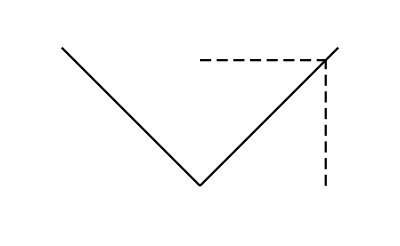

```mathematica
P1=Plot[x,{x,0,1.1},PlotStyle->Black];
P2=Plot[-x,{x,-1.1,0},PlotStyle->Black];
P3=Plot[1,{x,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
P4=ParametricPlot[{1,y},{y,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Show[P1,P2,P3,P4,PlotRange->{{-1.3,1.3},{-0.3,1.3}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.6/2.6,Frame->False,Ticks->None]
```

```mathematica
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r Cos[0],r Sin[0],1},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Black,Opacity[1],Dashing[{0.02,0.01}]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{1Cos[0],1Sin[0],r},{r,0,1},Axes->False, BoxRatios->{2,2,2},PlotStyle->{Black,Opacity[1],Dashing[{0.02,0.01}]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P2,P3,ViewPoint->{20,-10,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

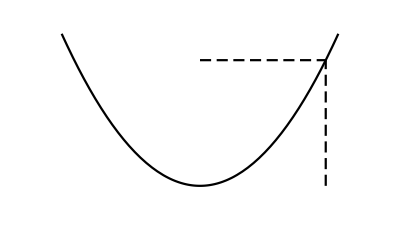

```mathematica
P1=Plot[x^2,{x,-1.1,1.1},PlotStyle->Black];
P3=Plot[1,{x,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
P4=ParametricPlot[{1,y},{y,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Show[P1,P3,P4,PlotRange->{{-1.3,1.3},{-0.3,1.3}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.6/2.6,Frame->False,Ticks->None]
```

```mathematica
P1=Plot3D[{x*y},{x,-1.2,1.2},{y,-1.2,1.2},Axes->False, BoxRatios->{1.2,1.2,1.44},PlotStyle->{Green,Opacity[0.9]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.8,0,0},{1.8,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.8},{0,0,1.8}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.8,0},{0,1.8,0}}]}},Axes->False,BoxRatios->{1.8,1.8,1.8}];
Show[G1,P1,ViewPoint->{-20,40,10},Boxed->False]
```

-Graphics3D-

```mathematica
P1=Plot3D[{x^2-y^2},{x,-1.2,1.2},{y,-1.2,1.2},Axes->False, BoxRatios->{1.2,1.2,1.44},PlotStyle->{Green,Opacity[0.9]},PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.8,0,0},{1.8,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.8},{0,0,1.8}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.8,0},{0,1.8,0}}]}},Axes->False,BoxRatios->{1.8,1.8,1.8}];
Show[G1,P1,ViewPoint->{10,20,10},Boxed->False]
```

-Graphics3D-

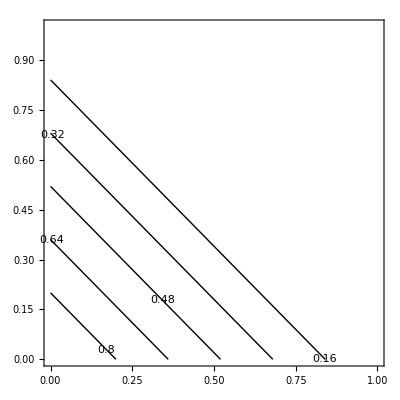

```mathematica
S0=ContourPlot[1-x-y,{x,0,1.0},{y,0,1-x},Ticks->None,ContourShading->None,ContourLabels->All,Contours->5]
```

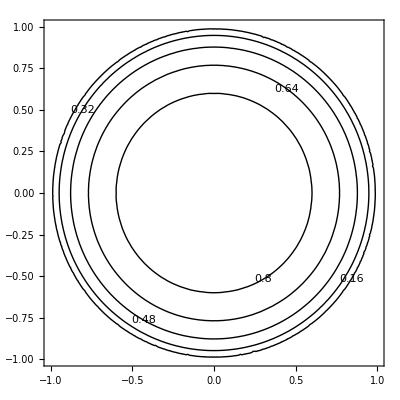

```mathematica
S0=ContourPlot[Sqrt[1-x^2-y^2],{x,-1,1},{y,-1,1},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,ContourShading->None,ContourLabels->All,Contours->5]
```

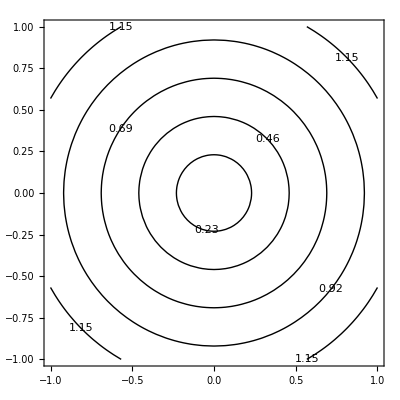

```mathematica
S0=ContourPlot[Sqrt[x^2+y^2],{x,-1,1},{y,-1,1},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,ContourShading->None,ContourLabels->All,Contours->5]
```

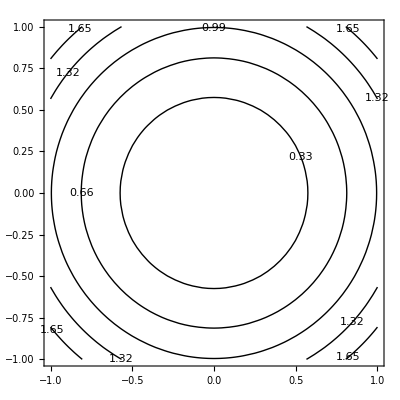

```mathematica
S0=ContourPlot[x^2+y^2,{x,-1,1},{y,-1,1},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,ContourShading->None,ContourLabels->All,Contours->5]
```

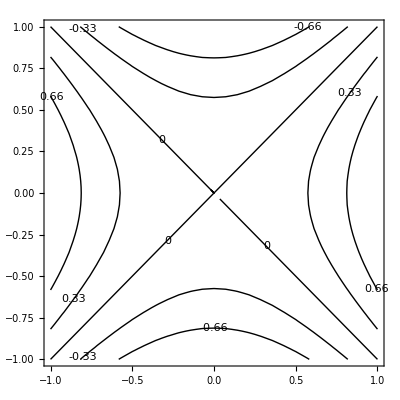

```mathematica
S0=ContourPlot[x^2-y^2,{x,-1,1},{y,-1,1},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,ContourShading->None,ContourLabels->All,Contours->5]
```

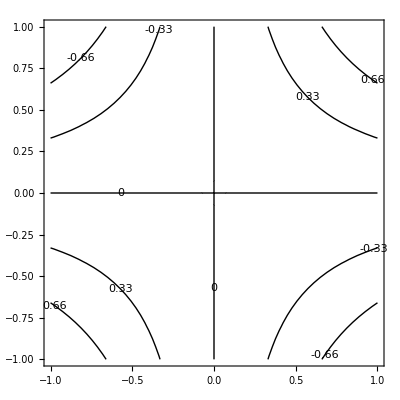

```mathematica
S0=ContourPlot[x*y,{x,-1,1},{y,-1,1},Axes->False, BoxRatios->{1,1,0.5},Mesh->0,ContourShading->None,ContourLabels->All,Contours->5]
```